# Parsing and interpretation of integration commands

## Introduction

This chapter exemplifies the use of Functional Parsers -- also known as Parser Combinators -- for the interpretation of a small Domain Specific Language (DSL) for symbolic and numeric integration commands.

The functional parsers implementations are based on the article “Functional Parsers” by Jeroen Fokker, [JF1].

The functional parsers presented form a monadic system. More explanations and references can be found in the Wikipedia article Parser Combinator, [Wk1].

It is assumed the readers of this chapter are at least somewhat familiar with the parsing problem, the Backus-Naur Form for grammar specifications, [Wk2], and the concept of definite integral in calculus.

### Setup

Here we load the paclet "FunctionalParsers", [AAp2]:

```mathematica
Needs["AntonAntonov`FunctionalParsers`"]
```

## Sentences

Suppose we want to make an interpreter of commands for single variable integrals calculation.

We can start by listing prototype sentences and then generalizing their form.

Here are some prototypes:

Calculate the integral of sin x over 0 to 1.

What is the integral of x^2+Log[x] for x in the interval 0 and 10?

Integrate Sin[x^2+5]

Integrate numerically 1/x+Sqrt[x] in the interval 4 and 10.

## General command structure

We can say the integration commands have four parts:

1. type of integration (numerical or symbolical),

2. function to be integration (integrand),

3. variable (optional can be implied),

4. range (optional).

Roughly speaking we have the following structure:

<command preamble> <integral type> <integrand> <variable> <range>

## Graph of the command structure

This graph represents the grammar of the integration commands we consider:
1. Branching represents alternatives or composition
2. The words and phrases and in quotes are tokens
3. The abstract rules are in angular brackets (“<xxx>”)
4. The dashed arrows mean “followed by”
5. Square brackets (“[xxx]”) are for optional parts
6. Examples are given as “free” text

-Graphics-

## How we do the parsing

We are going to program parsers for the grammar rules in the graph of the previous slide.

The graph follows closely the Extended Backus-Naur Form (EBNF), [Wk2].

Here is the EBNF for the integration command language we consider:

<request-preamble> = 'compute' | 'what' , 'is' ;
<compute> = <request-preamble> , [ 'the' ] ;
<integral-type> = [ 'numerical' | 'symbolic' ] , 'integral' ;
<integrate> = [ 'symbolically' | 'numerically' ] , 'integrate' | 'integrate' , ( 'numerically' | 'symbolically' ) ;
<function> = '_String' ;
<variable> = '_IdentifierString' ;
<range-named> =  'R' | 'R+' | 'R-' ;
<range-interval> = [ 'from' ] , '_WordString' , [ 'to' | 'and' ] , '_WordString';
<range> = ( [ 'in' | 'over' ] , [ 'the' ] , [ 'interval' ] ) , ( <range-interval> | <range-named> ) ;
<var-range-spec> = ( 'for' | 'of' ) , <variable> , <range> ;
<integral-request> = <compute> , <integral-type> , 'of' ;
<command1> = ( <integral-request> | <integrate> ) , <function> , ( <var-range-spec> | <range> ) ;
<command2> = ( <integral-request> | <integrate> ) , <function> ;
<command> = <command1> | <command2> ;

We are going to write a parser for each EBNF rule.

Later in the talk we are going to show that using the package FunctionalParsers.m we can generate the parsers from a string with the EBNF of the grammar.

## Parsing <compute>

The first grammar rule we consider is <compute> that has the <request-preamble> as sub-part.

<request-preamble> = 'compute' | 'what' , 'is' ;
<compute> = <request-preamble> , [ 'the' ] ;

Taking LHS of rule we remove the dashes, “-”, and put the prefix “p” in order to derive the symbol of parser corresponding to that rule.

Here is the parser for <request-preamble>:

```mathematica
pREQUESTPREAMBLE=ParseAlternativeComposition[ParseSymbol["compute"],ParseSequentialComposition[ParseSymbol["what"],ParseSymbol["is"]]]
```

ParseAlternativeComposition[If[Length[#1]>0&&compute===First[#1],{{Rest[#1],compute}},{}]&,ParseSequentialComposition[If[Length[#1]>0&&what===First[#1],{{Rest[#1],what}},{}]&,If[Length[#1]>0&&is===First[#1],{{Rest[#1],is}},{}]&]]

Which more compactly can be defines as:

```mathematica
pREQUESTPREAMBLE=ParseSymbol["compute"]⊕ParseSymbol["what"]⊗ParseSymbol["is"];
```

The symbol “⊕” is an infix notation shorthand of ParseAlternativeComposition.
The symbol “⊗” is an infix notation shorthand of ParseSequentialComposition.

Let us test the parser with the integration command string

```mathematica
icom="what is the integral of Sin[x] over 0 1";
```

which we split into tokens first:

```mathematica
pREQUESTPREAMBLE[StringSplit[icom]]
```

{{{the,integral,of,Sin[x],over,0,1},{what,is}}}

The parsing of <request-preamble> is successful, but in order to see than we need to explain the function parser definition.

## Parser definition

First definition: We define a parser type to be a function that transforms a list of characters or tokens into (1) an unparsed list of tokens and (2) a parse tree:

P: _String → {_String, _ParseTree }

or 

P: {_String...} → { {_String...}, _ParseTree }

It is better though to generalize this definition to allow a list of results:

P: {_String...} → { { {_String...}, _ParseTree }...}

(This is related to the so called “method of lists of success.”)

The functional parsers are categorized in the groups: basic, combinators, and transformers.
1. The basic parsers parse specified strings and strings adhering to predicates.
2. The combinator parsers allow sequential and alternative combinations of parsers.
3. The transformer parsers change the input or the output of the parsers that are transformed.

The parser ParseSymbol is a basic parser; ParseAlternativeComposition and ParseSequentialComposition are combinators.

## Parsing <compute>, continued

So far we have the parsing result:

```mathematica
pREQUESTPREAMBLE[StringSplit[icom]]
```

{{{the,integral,of,Sin[x],over,0,1},{what,is}}}

The parsing of <request-preamble> is successful. Looking at the grammar rules

<request-preamble> = 'compute' | 'what' , 'is' ;
<compute> = <request-preamble> , [ 'the' ] ;

we are ready to define <compute> that combines <request-preamble> with an optional “the”:

```mathematica
pCOMPUTE=pREQUESTPREAMBLE⊗ParseOption[ParseSymbol["the"]];
```

The definition of <compute> uses another combinator parser ParseOption for optional tokens.

The parsed result contains two possible parsings, one with “the“ parsed, and one without:

```mathematica
pCOMPUTE[StringSplit[icom]]
```

{{{integral,of,Sin[x],over,0,1},{{what,is},{the}}},{{the,integral,of,Sin[x],over,0,1},{{what,is},{}}}}

We can use the parser combinator ParseShortest to select the one parsed the token “the”:

```mathematica
ParseShortest[pCOMPUTE][StringSplit[icom]]
```

{{{integral,of,Sin[x],over,0,1},{{what,is},{the}}}}

## Parsing <integral-type> and <integral-request>

The definition of the parser <integral-type>

```mathematica
pINTEGRALTYPE=ParseOption[ParseSymbol["numerical"]⊕ParseSymbol["symbolic"]]⊗ParseSymbol["integral"];
```

follows directly the EBNF rule

<integral-type> = [ 'numerical' | 'symbolic' ] , 'integral' ;

Now we can define <integral-request>

```mathematica
pINTEGRALREQUEST=pCOMPUTE⊗pINTEGRALTYPE;
```

```mathematica
icom
```

what is the integral of Sin[x] over 0 1

```mathematica
pINTEGRALREQUEST[StringSplit[icom]]
```

{{{of,Sin[x],over,0,1},{{{what,is},{the}},{{},integral}}}}

## Picking only the important part

In many cases the semantic meaning of a grammar rule can be identified only by some part of the parsed input. 
For example, in the context of the integration language the phrases “compute” and “what is” are needed in order to extend the number of admissible sentences, but as soon as they are parsed they are no longer of interest. What is of interest is to know what type of integration is requested: numerical or symbolical. (If the type is not explicitly specified we are going to interpret as “symbolic”.)

Instead of using ParseSequentialComposition (⊗) in the parser definition for the rule <integration-request> we can use ParseSequentialCompositionPickRight (⊳) :

```mathematica
pINTEGRALREQUEST=pCOMPUTE⊳pINTEGRALTYPE;
```

```mathematica
pINTEGRALREQUEST[StringSplit[icom]]
```

{{{of,Sin[x],over,0,1},{{},integral}}}

Compare with the parsing with the previous definition using ParseSequentialComposition (⊗) :

```mathematica
(pCOMPUTE⊗pINTEGRALTYPE)[StringSplit[icom]]
```

{{{of,Sin[x],over,0,1},{{{what,is},{the}},{{},integral}}}}

If the type of integration is explicitly specified as in

```mathematica
nicom="what is the numerical integral of Sin[x] over 0 1";
```

then the new definition of <integral-request> outputs:

```mathematica
pINTEGRALREQUEST[StringSplit[nicom]]
```

{{{of,Sin[x],over,0,1},{{numerical},integral}}}

## Transforming the parser results

Obviously we can (and should) go further and throw away also “integral“ using ParseSequentialCompositionPickLeft (⊲) as in

```mathematica
pINTEGRALTYPE=ParseOption[ParseSymbol["numerical"]⊕ParseSymbol["symbolic"]]⊲ParseSymbol["integral"];
pINTEGRALREQUEST=pCOMPUTE⊳pINTEGRALTYPE;
```

```mathematica
nicom
pINTEGRALREQUEST[StringSplit[nicom]]
```

what is the numerical integral of Sin[x] over 0 1

{{{of,Sin[x],over,0,1},{numerical}}}

But now if do not specify explicitly the integration type we are going to have an empty successfully parsed part:

```mathematica
icom
pINTEGRALREQUEST[StringSplit[icom]]
```

what is the integral of Sin[x] over 0 1

{{{of,Sin[x],over,0,1},{}}}

Of course when we interpret the parsed output we can imply from no integral type specification that the integration is symbolic, but it is better if we can modify the parsed output of the rule <integral-type> to indicate the integration type.

This can be done using the parser transformer ParseApply (infix shorthand ⊙) that applies a function to the successfully parsed part.

```mathematica
pINTEGRALTYPE=ParseApply[IType,ParseOption[ParseSymbol["numerical"]⊕ParseSymbol["symbolic"]]⊲ParseSymbol["integral"]];
pINTEGRALREQUEST=pCOMPUTE⊳pINTEGRALTYPE;
```

```mathematica
pINTEGRALREQUEST[StringSplit[icom]]
```

{{{of,Sin[x],over,0,1},IType[{}]}}

```mathematica
pINTEGRALREQUEST[StringSplit[nicom]]
```

{{{of,Sin[x],over,0,1},IType[{numerical}]}}

## Transforming the parser results, continued

Let us apply a more complicated function to the rule <integral-type>. For example,

```mathematica
pINTEGRALTYPE=
ParseApply[
IType[#/.{{}->"Symbolic",_->"Numeric"}]&,ParseOption[ParseSymbol["numerical"]⊕ParseSymbol["symbolic"]]⊲ParseSymbol["integral"]];
pINTEGRALREQUEST=pCOMPUTE⊳pINTEGRALTYPE;
```

With the new definition we get

```mathematica
icom
pINTEGRALREQUEST[StringSplit[icom]]
```

what is the integral of Sin[x] over 0 1

{{{of,Sin[x],over,0,1},IType[Symbolic]}}

```mathematica
nicom
pINTEGRALREQUEST[StringSplit[nicom]]
```

what is the numerical integral of Sin[x] over 0 1

{{{of,Sin[x],over,0,1},IType[Numeric]}}

## Other basic parsers

The only basic parse we used so far is ParseSymbol. A very often used one is ParsePredicate.

Suppose we want to parse a number string. Using ParsePredicate we can define the number parser as

```mathematica
pNumber=ParsePredicate[StringMatchQ[#,NumberString]&]
```

ParsePredicate[StringMatchQ[#1,NumberString]&]

ParserPredicate takes a function as an argument and the parsing is successful it that functions returns True.

```mathematica
pNumber[{"3432"}]
```

{{{},3432}}

Note that the parsed result is a string

```mathematica
%//FullForm
```

List[List[List[],"3432"]]

We can use ParseApply to convert to a number in Mathematica:

```mathematica
pNumber=ToExpression⊙ParsePredicate[StringMatchQ[#,NumberString]&]
```

ParseApply[ToExpression,ParsePredicate[StringMatchQ[#1,NumberString]&]]

```mathematica
pNumber[{"3432"}]
%//FullForm
```

{{{},3432}}

List[List[List[],3432]]

## Other basic parsers, continued

Here is the full list of the basic parser in the package FunctionalParsers.m :

ParseSymbol[s] 		parses a specified symbol s.
ParseToken[t] 			parses the token t.
ParsePredicate[p] 	parses strings that give True for the predicate p.
ParseEpsilon 			parses and empty string.
ParseSucceed[v] 		does not consume input and always returns v.
ParseFail 				fails to recognize any input string.

## Other parser combinators

Here is a couple of more useful parser combinators: ParseMany and ParseListOf.

Suppose we want to parse sequence of numbers. It is easy to define a parser doing that using ParseMany and ParsePredicate:

```mathematica
pNumber=ToExpression⊙ParsePredicate[StringMatchQ[#,NumberString]&];
pNumberSeq=ParseMany[pNumber];
```

```mathematica
ParseJust[pNumberSeq][StringSplit["234 232 -532"]]
```

{{{},{234,232,-532}}}

We parsed with the parser transformer ParseJust in order to get results that parsed out the sequence completely.

If we want to parse a sequence of numbers separated by, say, semicolon we can use ParseListOf:

```mathematica
pNumberList=ParseListOf[pNumber,ParseSymbol[";"]];
```

```mathematica
ParseJust[pNumberList][StringSplit["234 ; 232 ; -532"]]
```

{{{},{234,232,-532}}}

Two other related parsers are ParseChainLeft and ParseChainRight :

```mathematica
ParseJust[ParseChainLeft[pNumber,ParseSymbol["+"]]][StringSplit["234 + 232 + -532"]]
```

{{{},+[+[234,232],-532]}}

```mathematica
ParseJust[ParseChainRight[pNumber,ParseSymbol["+"]]][StringSplit["234 + 232 + -532"]]
```

{{{},+[234,+[232,-532]]}}

## The rest of the integration grammar rules

At this point it should be clear how we proceed with defining the rest of the grammar rules of the integration request language.

In order to keep things simple the integration function is assumed to be a Mathematica expression with no spaces within it.

For example

```mathematica
ParseJust[pCOMMAND][StringSplit["integrate Sin[x]Log[x]/3 over 0 1"]]
```

{{{},ICommand[{{IType[{}],{}},{IFunc[Sin[x]Log[x]/3],{IRange[{0,1}],{}}}}]}}

The type of the integration is going to be implied to be symbolic if IType has an empty list.

For the grammar rules <variable> and <range> we use IVar and IRange respectively:

```mathematica
ParseJust[pCOMMAND][StringSplit["compute the numerical integral of Log[x] of x from 0 to 10"]]
```

{}

Next we are going to generate automatically the parsers using the EBNF grammar.

## Parser generation

Using the EBNF of the grammar of the integration commands language we can automatically generate the parsers for its grammar rules using the function GenerateParsersFromEBNF provided by the package FunctionalParsers.m .

In the current version of the EBNF parser functions there is a requirement that all elements of the parsed EBNF forms have to be separated by space.

The EBNF grammar string can have the pick-left and pick-right combinators (<& and &> respectively) and a ParseApply specification can be given within the form “<rhs> = parsers <@ transformer” . The application of functions can be done over the whole definition of an EBNF non-terminal symbol, not over the individual parts.

Here is the grammar of the integration language:

```mathematica
integrationGrammar="
<command> = <command1> | <command2> <@ ICommand ;
<command1> = ( <integral-request> | <integrate> ) , <function> , ( <var-range-spec> | <range> ) ;
<command2> = ( <integral-request> | <integrate> ) , <function> ;
<request-preamble> = 'compute' | 'what' , 'is' ;
<compute> = <request-preamble> , [ 'the' ] ;
<integral-type> = [ 'numerical' | 'symbolic' ] <& 'integral' <@ IType ;
<integrate> = [ 'symbolically' | 'numerically' ] <& 'integrate' | 'integrate' &> ( 'numerically' | 'symbolically' ) <@ IType ;
<function> = '_String' <@ IFunc ;
<var> = '_IdentifierString' <@ IVar ;
<range-named> =  'R' | 'R+' | 'R-' <@ IRange ;
<range-interval> = [ 'from' ] &> '_WordString' , [ 'to' | 'and' ] &> '_WordString' <@ IRange ;
<range> = ( [ 'in' | 'over' ] , [ 'the' ] , [ 'interval' ] ) &> ( <range-interval> | <range-named> ) ;
<var-range-spec> = ( 'for' | 'of' ) &> <var> , <range> ;
<integral-request> = <compute> &> <integral-type> <& 'of' ;
";
```

## Parser generation, continued 1

It is beneficial to examine the random sentences with the grammar we have developed.

```mathematica
SeedRandom[4467];
Multicolumn[Sort[GrammarRandomSentences[GrammarNormalize[integrationGrammar],30]],2]
```

compute integral of jdt | integrate numerically msg9nj for zcm in the interval from qc24 and 4xg
compute symbolic integral of o2efqi | integrate oqj
compute symbolic integral of wnls | integrate pqxhbe9
compute the integral of dkvqrl39 | integrate symbolically djwk4g5yap
compute the integral of tgcbpj87 | integrate yro38 interval yu6 wpu93v
compute the symbolic integral of ab4 | numerically integrate 9wzl8k for vcabgelxs the from ol914yj nxvep
compute the symbolic integral of az1oplftx4 for krmcpbiyt R+ | numerically integrate se0b
compute the symbolic integral of v5ky71 | symbolically integrate 2abw9tod8
integrate 9ugasr for nzaowceiyj over the interval from eymj dszm | symbolically integrate xtk7v over from lc0 58uqtk12
integrate b61j of okrjyhgt in the R- | what is integral of cd0uor7lq the from hwxd31ysze to k7c1y
integrate ly2t8ecn4 | what is integral of fc6
integrate numerically bay20s8t | what is integral of fgnc7 interval R+
integrate numerically doaqlry | what is integral of srqbdx6pne the R
integrate numerically fkxyinq over the mcojq2nk5 hufca1q | what is the integral of la7
integrate numerically jhyzb7x43 ctj smy231 | what is the integral of n3zju8 of ztqjckxl the interval R-

## Parser generation, continued 2

Let us see how the parsed tree of the grammar looks like:

```mathematica
code=ToTokens[integrationGrammar];
Magnify[ParseEBNF[code],0.7]
```

{{{},EBNF[{EBNFRule[{{<command>,EBNFAlternatives[{EBNFSequence[EBNFNonTerminal[<command1>]],EBNFSequence[EBNFNonTerminal[<command2>]]}]},{<@,ICommand}}],EBNFRule[{{<command1>,EBNFAlternatives[{EBNFSequence[,[EBNFAlternatives[{EBNFSequence[EBNFNonTerminal[<integral-request>]],EBNFSequence[,[EBNFNonTerminal[<integrate>],EBNFOption[EBNFAlternatives[{EBNFSequence[&>[EBNFTerminal['and'],EBNFNonTerminal[<plot>]]]}]]]]}],,[EBNFNonTerminal[<function>],,[EBNFAlternatives[{EBNFSequence[EBNFNonTerminal[<var-range-spec>]],EBNFSequence[EBNFNonTerminal[<range>]]}],EBNFOption[EBNFAlternatives[{EBNFSequence[&>[EBNFTerminal['and'],EBNFNonTerminal[<plot>]]]}]]]]]]}]},;}],EBNFRule[{{<command2>,EBNFAlternatives[{EBNFSequence[,[EBNFAlternatives[{EBNFSequence[EBNFNonTerminal[<integral-request>]],EBNFSequence[EBNFNonTerminal[<integrate>]]}],EBNFNonTerminal[<function>]]]}]},;}],EBNFRule[{{<request-preamble>,EBNFAlternatives[{EBNFSequence[EBNFTerminal['compute']],EBNFSequence[,[EBNFTerminal['what'],EBNFTerminal['is']]]}]},;}],EBNFRule[{{<compute>,EBNFAlternatives[{EBNFSequence[,[EBNFNonTerminal[<request-preamble>],EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['the']]}]]]]}]},;}],EBNFRule[{{<integral-type>,EBNFAlternatives[{EBNFSequence[<&[EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['numerical']],EBNFSequence[EBNFTerminal['symbolic']]}]],EBNFTerminal['integral']]]}]},{<@,IType}}],EBNFRule[{{<integrate>,EBNFAlternatives[{EBNFSequence[<&[EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['symbolically']],EBNFSequence[EBNFTerminal['numerically']]}]],EBNFTerminal['integrate']]],EBNFSequence[&>[EBNFTerminal['integrate'],EBNFAlternatives[{EBNFSequence[EBNFTerminal['numerically']],EBNFSequence[EBNFTerminal['symbolically']]}]]]}]},{<@,IType}}],EBNFRule[{{<function>,EBNFAlternatives[{EBNFSequence[EBNFTerminal['_String']]}]},{<@,IFunc}}],EBNFRule[{{<var>,EBNFAlternatives[{EBNFSequence[EBNFTerminal['_IdentifierString']]}]},{<@,IVar}}],EBNFRule[{{<range-named>,EBNFAlternatives[{EBNFSequence[EBNFTerminal['R']],EBNFSequence[EBNFTerminal['R+']],EBNFSequence[EBNFTerminal['R-']]}]},{<@,IRange}}],EBNFRule[{{<range-interval>,EBNFAlternatives[{EBNFSequence[&>[EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['from']]}]],,[EBNFTerminal['_WordString'],&>[EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['to']],EBNFSequence[EBNFTerminal['and']]}]],EBNFTerminal['_WordString']]]]]}]},{<@,IRange}}],EBNFRule[{{<range>,EBNFAlternatives[{EBNFSequence[&>[EBNFAlternatives[{EBNFSequence[,[EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['in']],EBNFSequence[EBNFTerminal['over']]}]],,[EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['the']]}]],EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['interval']]}]]]]]}],EBNFAlternatives[{EBNFSequence[EBNFNonTerminal[<range-interval>]],EBNFSequence[EBNFNonTerminal[<range-named>]]}]]]}]},;}],EBNFRule[{{<var-range-spec>,EBNFAlternatives[{EBNFSequence[&>[EBNFAlternatives[{EBNFSequence[EBNFTerminal['for']],EBNFSequence[EBNFTerminal['of']]}],,[EBNFNonTerminal[<var>],EBNFNonTerminal[<range>]]]]}]},;}],EBNFRule[{{<integral-request>,EBNFAlternatives[{EBNFSequence[&>[EBNFNonTerminal[<compute>],<&[EBNFNonTerminal[<integral-type>],EBNFTerminal['of']]]]}]},;}],EBNFRule[{{<plot>,EBNFAlternatives[{EBNFSequence[<&[EBNFTerminal['plot'],EBNFOption[EBNFAlternatives[{EBNFSequence[EBNFTerminal['it']]}]]]]}]},{<@,IPlot}}]}]}}

## Parser generation, continued 3

Let us generate the grammars with GenerateParsersFromEBNF:

```mathematica
code=ToTokens[integrationGrammar];
res=GenerateParsersFromEBNF[code];
LeafCount[res]
```

969

and tabulate the parsed results of a set of commands with ParsingTestTable:

```mathematica
commands={
"compute the symbolic integral of Sin[x]*x^2 over 0 to 10",
"what is the numerical integral of t^4+Log[t] for t in the interval 0 to 10",
"integrate Sin[x]*x^2 over a b",
"integrate Exp[-x] over R+"
};
ParsingTestTable[ParseShortest[pCOMMAND],commands,"Layout"->"Vertical"]//Magnify[#,0.8]&
```

1 | command: | compute the symbolic integral of Sin[x]*x^2 over 0 to 10
 | parsed: | ICommand[{IType[symbolic],{IFunc[Sin[x]*x^2],{IRange[{0,10}],{}}}}]
 | residual: | {}
2 | command: | what is the numerical integral of t^4+Log[t] for t in the interval 0 to 10
 | parsed: | ICommand[{IType[numerical],{IFunc[t^4+Log[t]],{{IVar[t],IRange[{0,10}]},{}}}}]
 | residual: | {}
3 | command: | integrate Sin[x]*x^2 over a b
 | parsed: | ICommand[{{IType[{}],{}},{IFunc[Sin[x]*x^2],{IRange[{a,b}],{}}}}]
 | residual: | {}
4 | command: | integrate Exp[-x] over R+
 | parsed: | ICommand[{{IType[{}],{}},{IFunc[Exp[-x]],{IRange[R+],{}}}}]
 | residual: | {}

## Interpretation

After we have generated the parsers of the integration requests grammar we have to write an interpreter of the parsed results.

Because of the way the parsing results are structured we can just write a definition for the function ICommand and the integrals are going to be computed during the parsing with pCOMMAND.

Instead, we are going to write a function ICommandInterpreter and use another function, InterpretWithContext (also provided by the package FunctionalParsers.m) to trigger the computation of the integrals.

```mathematica
ICommandInterpreter[parsed_]:=
Block[{op,func,var,range},
op=Flatten[Cases[parsed,IType[s_]:>s,∞]];
op=
Which[
MemberQ[op,"numerical"]||MemberQ[op,"numerically"],NIntegrate,
True,Integrate
];
func=ToExpression@Flatten[Cases[parsed,IFunc[s_]:>s,∞]]⟦1⟧;
var=Flatten@Cases[parsed,IVar[s_]:>s,∞];
If[Length[var]>0,
var=ToExpression@var⟦1⟧,
var=ToExpression@Flatten[Cases[func,s_Symbol/;!NumericQ[s],∞]]⟦1⟧
];
range=Flatten[Cases[parsed,IRange[s_]:>s,∞]];
If[Length[range]==0,
Integrate[func,x],
range=Replace[range,{{"R"}->{"-Infinity","Infinity"},{"R+"}->{"0","Infinity"},{"R-"}->{"-Infinity","0"}}];
range=ToExpression@range;
op[func,Evaluate[Prepend[range,var]]]
]
];
```

## Interpretation, continued 1

The function InterpretWithContext returns the interpretation of the input together with a list of rules of the context data if such data is given.

```mathematica
InterpretWithContext[
ParsingTestTable[ParseShortest[pCOMMAND],commands,"Layout"->"Vertical"],{ICommand->ICommandInterpreter}]//Magnify[#,0.8]&
```

{1 | command: | compute the symbolic integral of Sin[x]*x^2 over 0 to 10
 | parsed: | -2-98 Cos[10]+20 Sin[10]
 | residual: | {}
2 | command: | what is the numerical integral of t^4+Log[t] for t in the interval 0 to 10
 | parsed: | 20013.
 | residual: | {}
3 | command: | integrate Sin[x]*x^2 over a b
 | parsed: | (-2+a^2) Cos[a]-(-2+b^2) Cos[b]-2 a Sin[a]+2 b Sin[b]
 | residual: | {}
4 | command: | integrate Exp[-x] over R+
 | parsed: | 1
 | residual: | {},{}}

## Interpretation, continued 2

Here is a different set of integration commands:

```mathematica
commands={
"integrate symbolically Sin[x]*x^2 over a b",
"compute the numerical integral of Sin[x] for x over 0 to 10",
"integrate symbolically x+Sqrt[x] in the interval m0 and m1",
"compute the integral of Log[x] of x from 0 to r"
};
```

Now let us parse the integration commands using also data values for the context of interpretation.

```mathematica
InterpretWithContext[
ParsingTestTable[ParseShortest[pCOMMAND],commands,"Layout"->"Vertical"],{"data"->{a->A,b->B,m0->12,m1->100},"functions"->{ICommand->ICommandInterpreter}}]//Magnify[#,0.8]&
```

{1 | command: | integrate symbolically Sin[x]*x^2 over a b
 | parsed: | (-2+A^2) Cos[A]-(-2+B^2) Cos[B]-2 A Sin[A]+2 B Sin[B]
 | residual: | {}
2 | command: | compute the numerical integral of Sin[x] for x over 0 to 10
 | parsed: | 1.83907
 | residual: | {}
3 | command: | integrate symbolically x+Sqrt[x] in the interval m0 and m1
 | parsed: | 16784/3-16 √3
 | residual: | {}
4 | command: | compute the integral of Log[x] of x from 0 to r
 | parsed: | r (-1+Log[r])
 | residual: | {},{a→A,b→B,m0→12,m1→100}}

## Interpretation, continued 3

To summarize the interpretation:

1. The context is given as a list of rules

2. There are two forms for the context rules:

{(_Symbol->_)..} 
 {"data"->{(_Symbol->_)...}, "functions"->{(_Symbol->_)...}}

3. If during the interpretation the context functions change the context data the result of InterpretWithContext will return the changed data.

## Discussion

The automatic generation of parsers from a grammar specification is very useful.

Large grammars would demand too much book keeping of the parsers for them. Automatic generation of parsers definitely helps.

As an example let us consider a change in the integration requests language to include the sub-command of plotting the integrand over the specified integration range. We want to be able to interpret sentences like these:

compute the integral of Log[x] of x from 0 to 10 and plot it

integrate and plot Sin[x]*x^2 over 0 1

We can just extend the grammar, re-generate the parsers, and provide interpretation for plotting clauses if they are present.

Here is the grammar with “plot it” added (the new symbol <plot> is used in <command1>):

```mathematica
integrationGrammar="
<command> = <command1> | <command2> <@ ICommand ;
<command1> = ( <integral-request> | <integrate> , [ 'and' &> <plot> ] ) , <function> , ( <var-range-spec> | <range> ) , [ 'and' &> <plot> ] ;
<command2> = ( <integral-request> | <integrate> ) , <function> ;
<request-preamble> = 'compute' | 'what' , 'is' ;
<compute> = <request-preamble> , [ 'the' ] ;
<integral-type> = [ 'numerical' | 'symbolic' ] <& 'integral' <@ IType ;
<integrate> = [ 'symbolically' | 'numerically' ] <& 'integrate' | 'integrate' &> ( 'numerically' | 'symbolically' ) <@ IType ;
<function> = '_String' <@ IFunc ;
<var> = '_IdentifierString' <@ IVar ;
<range-named> = 'R' | 'R+' | 'R-' <@ IRange ;
<range-interval> = [ 'from' ] &> '_WordString' , [ 'to' | 'and' ] &> '_WordString' <@ IRange ;
<range> = ( [ 'in' | 'over' ] , [ 'the' ] , [ 'interval' ] ) &> ( <range-interval> | <range-named> ) ;
<var-range-spec> = ( 'for' | 'of' ) &> <var> , <range> ;
<integral-request> = <compute> &> <integral-type> <& 'of' ;
<plot> = 'plot' <& [ 'it' ] <@ IPlot ;
";
```

## Discussion, continued 1

Here are some random sentences (commands) generated with the grammar we defined:

```mathematica
SeedRandom[2387];
Multicolumn[Sort@GrammarRandomSentences[GrammarNormalize[integrationGrammar],30],2]
```

compute integral of 6f3jw5ki R | integrate symbolically xjpzauw
compute integral of 75qu | integrate symbolically xriqu0b5a the from ajp45c to xkc0ri8 and plot
compute integral of iuq60t R- | numerically integrate 1fcrmy5qa8
compute numerical integral of i4jpt over the interval from m9hs4zaqt and gvxp2u and plot | numerically integrate and plot it 2qf4vz the interval from 5shzcvnfd to a0r2u
compute symbolic integral of 2xec78ho4q | symbolically integrate e4j
compute the integral of lek over the R- | symbolically integrate f4ip
compute the numerical integral of 6orw1cpb of xtjldhnp the interval R+ and plot it | what is integral of egc the interval R-
integrate 0vi8e3f7ls | what is integral of yt7uf8gzmk
integrate 3yokq2z4a9 | what is numerical integral of u97 for goewcsdux the interval 3yk9tfq7 to e3liptc0a9
integrate 7pr1s2 | what is symbolic integral of 09dzk for ljcpe over interval R+
integrate and plot it h5l0kcsdv6 over interval R- | what is the integral of 1cg5ldan the R-
integrate m27856 over the 2j0 to sw1bifu | what is the integral of 7plnyx in the interval from 7p5 jafh5dsq and plot it
integrate symbolically 01r5wni | what is the numerical integral of ih49kty0o
integrate symbolically qyt8m | what is the symbolic integral of gxlwdft
integrate symbolically sfoz3wy | what is the symbolic integral of m5tcwxh of ylihpbwu the interval from qrl6 kzb9xf and plot

## Discussion, continued 2

And here is the interpretation function that both integrates and plots:

```mathematica
ICommandPlotInterpreter::noplot="Cannot plot for a symbolic integral specification.";
ICommandPlotInterpreter[parsed_]:=
Block[{op,func,var,range},
op=Flatten[Cases[parsed,IType[s_]:>s,∞]];
op=
Which[
MemberQ[op,"numerical"]||MemberQ[op,"numerically"],NIntegrate,
True,Integrate
];
func=ToExpression@Flatten[Cases[parsed,IFunc[s_]:>s,∞]]⟦1⟧;
var=Flatten@Cases[parsed,IVar[s_]:>s,∞];
If[Length[var]>0,
var=ToExpression@var⟦1⟧,
var=ToExpression@Flatten[Cases[func,s_Symbol/;!NumericQ[s],∞]]⟦1⟧
];
range=Flatten[Cases[parsed,IRange[s_]:>s,∞]];
If[Length[range]==0,
If[Count[parsed,IPlot[_],∞]>0,Message[ICommandInterpreter::noplot]];
{Integrate[func,x]},
(*ELSE*)
range=Replace[range,{{"R"}->{"-Infinity","Infinity"},{"R+"}->{"0","Infinity"},{"R-"}->{"-Infinity","0"}}];
range=ToExpression@range;
If[Count[parsed,IPlot[_],∞]>0,
If[!VectorQ[range,NumberQ],
Message[ICommandPlotInterpreter::noplot];
{op[func,Evaluate[Prepend[range,var]]]},
{op[func,Evaluate[Prepend[range,var]]],Plot[func,Evaluate[Prepend[range,var]]]}
],
(*ELSE*)
{op[func,Evaluate[Prepend[range,var]]]}
]
]
];
```

## Discussion, continued 3

Let us try the new functionality out with several integration-and-plot commands:

```mathematica
commands={
"compute the integral of Log[x] of x from 0 to 10 and plot it",
"integrate and plot Sin[x]*x^2 over 0 1",
"integrate and plot Sin[x]*x^2 over a b"
};
ParsingTestTable[ParseShortest[pCOMMAND],commands,"Layout"->"Vertical"]
```

1 | command: | compute the integral of Log[x] of x from 0 to 10 and plot it
 | parsed: | ICommand[{IType[{}],{IFunc[Log[x]],{{IVar[x],IRange[{0,10}]},IPlot[plot]}}}]
 | residual: | {}
2 | command: | integrate and plot Sin[x]*x^2 over 0 1
 | parsed: | ICommand[{{IType[{}],IPlot[plot]},{IFunc[Sin[x]*x^2],{IRange[{0,1}],{}}}}]
 | residual: | {}
3 | command: | integrate and plot Sin[x]*x^2 over a b
 | parsed: | ICommand[{{IType[{}],IPlot[plot]},{IFunc[Sin[x]*x^2],{IRange[{a,b}],{}}}}]
 | residual: | {}

ICommandPlotInterpreter::noplot: Cannot plot for a symbolic integral specification.

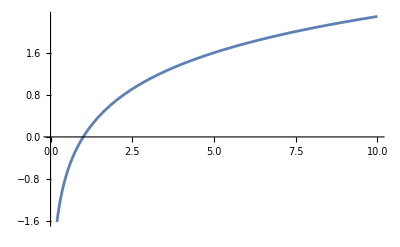
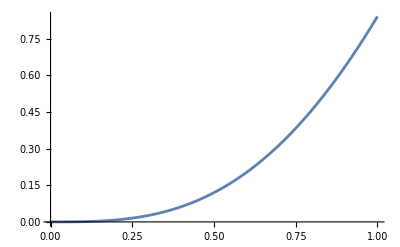
{1 | command: | compute the integral of Log[x] of x from 0 to 10 and plot it
 | parsed: | {10 (-1+Log[10]),-Graphics-}
 | residual: | {}
2 | command: | integrate and plot Sin[x]*x^2 over 0 1
 | parsed: | {-2+Cos[1]+2 Sin[1],-Graphics-}
 | residual: | {}
3 | command: | integrate and plot Sin[x]*x^2 over a b
 | parsed: | {(-2+a^2) Cos[a]-(-2+b^2) Cos[b]-2 a Sin[a]+2 b Sin[b]}
 | residual: | {},{}}

```mathematica
InterpretWithContext[
ParsingTestTable[ParseShortest[pCOMMAND],commands,"Layout"->"Vertical"],{ICommand->ICommandPlotInterpreter}]//Magnify[#,0.8]&
```

(We get the message “noplot” for the last integration request.)

## Summary

We defined an EBNF grammar for an integration requests language and showed how parsers for it can be implemented using the paclet "FunctionalParsers", [AAp2] .

The system of parsers of the package has

1. Tokenizer

2. Elementary parsers

3. Parser combinators

4. Parser transformers

5. Binding for infix notation

6. Functions for automatic parser generation

7. A function for interpretation with context

We discussed the automatic parser generation and its usefulness for grammar extension and bookkeeping.

## References

### Articles

[AA1] Anton Antonov, Functional parsers for an integration requests language grammar, (2014), MathematicaForPrediction at GitHub.

[Wk1] Wikipedia entry, "Parser Combinator".

[Wk2] Wikipedia entry, "Extended Backus-Naur Form".

### Packages, paclets

[AAp1] Anton Antonov, Functional parsers Mathematica package, (2014), MathematicaForPrediction at GitHub.

[AAp2] Anton Antonov, FunctionalParsers, (2023), Wolfram Language Paclet Repository.

Related Guides

BookChapters

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/SoftwareDesignMethodsWithWLBook

AntonAntonov`SoftwareDesignMethodsWithWLBook`

AntonAntonov/SoftwareDesignMethodsWithWLBook/tutorial/Parsingandinterpretationofintegrationcommands

### Keywords

Functional parsers

Grammar

Backus-Naur Form

BNF

Integration

Numerical integration

Symbolic integration